## Definitions

```mathematica
MSol=1.989*10^30;
G=6.674*10^-11;
AU=1.496*10^11;
YRtoS=(365)*(24)*(60)*(60);

MA=2.20*MSol;
MB=0.987*MSol;
τ=50.09;

μ=(MA*MB)/(MA+MB);
γ=G*MA*MB;
```

## semi-major axis

```mathematica
a=((τ*YRtoS)^2(μ/γ 4 π^2)^-1)^(1/3)
```

2.99033×10^12

```mathematica
a*AU^-1
```

19.9889

## orbital parameters a and ϵ

```mathematica
rmin=7.989*AU;
```

```mathematica
ϵ=(a-rmin)/a
c=rmin*(1+ϵ)
c*AU^-1
```

0.600327

1.91264×10^12

12.785

## plotting the stars motions

### define the radial equation r

```mathematica
r[ϕ_]:=c/(ϵ*Cos[ϕ]+1);
```

### define rA and rB

```mathematica
rA[ϕ_]:=MB/(MA+MB)r[ϕ];
rB[ϕ_]:=-MA/(MA+MB)r[ϕ];
```

### define in cartesian

```mathematica
xA[ϕ_]:=rA[ϕ]*Cos[ϕ]*AU^-1;
yA[ϕ_]:=rA[ϕ]*Sin[ϕ]*AU^-1;

xB[ϕ_]:=rB[ϕ]*Cos[ϕ]*AU^-1;
yB[ϕ_]:=rB[ϕ]*Sin[ϕ]*AU^-1;
```

### plot

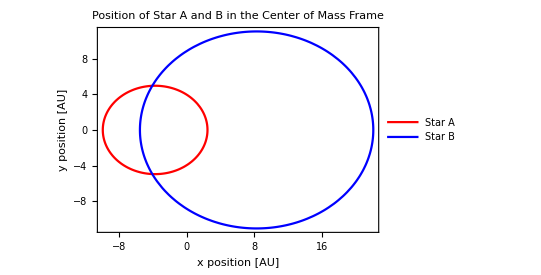

```mathematica
ParametricPlot[
{{xA[ϕ],yA[ϕ]},{xB[ϕ],yB[ϕ]}},
{ϕ,0,2π},
PlotLegends->{"Star A","Star B"},
PlotStyle->{{Red,Thick},{Blue,Thick}},
Frame->True,
FrameLabel->{"x position [AU]", "y position [AU]"},
PlotLabel->"Position of Star A and B in the Center of Mass Frame",
LabelStyle->Black,
FrameStyle->Black
]
```